```mathematica
<<MaTeX`
```

```mathematica
(* markers for plotting *)
markerCirc = Graphics[{#, EdgeForm[{#}], FaceForm[Opacity[.075]], Disk[]}]&;
markerDisk = Graphics[{#,  EdgeForm[{#}], FaceForm[Opacity[0.7]], Disk[]}]&;
markerTriangle =  Graphics[{#,  EdgeForm[{#}], FaceForm[Opacity[.7]], Triangle[{{0,0},{0.5, (√3)/2},{1,0}}]}]&;
(* markers examples *)
GraphicsRow[{ markerCirc[Gray],markerDisk[Gray], markerTriangle[Gray] }, ImageSize->100]
(* color for train/test points *)
testpntsCol= RGBColor[0.07,0.66,1];
trainpntsCol = RGBColor[1,0.36,0.08];
```

-Graphics-

```mathematica
(* training / test points *)
trainPoints = {0.1->0.5, 0.2 ->0.2, 0.4->0.1, 0.5->0.25, 0.8->0.47,0.9->0.48, 1-> 0.5};
testPoints = {0.3, 0.7};
```

```mathematica
(* fit GP *)
gp=Predict[trainPoints,Method->"GaussianProcess"]
```

PredictorFunction[…]

```mathematica
maxy = 1;
lines=Line[{{#,-maxy},{#,maxy}}]&/@testPoints;
lineStyle = {Red, Dashed};
```

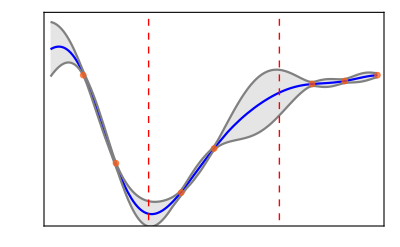

```mathematica
xTicks={0,  0.2,  0.4, 0.6,  0.8, 1};
yTicks = {0,  0.2, 0.4, 0.6};
plot = Show[
Plot[{gp[x],gp[x]+StandardDeviation[gp[x, "Distribution"]], gp[x]-StandardDeviation[gp[x, "Distribution"]]}, {x, 0, 1}, 
PlotStyle->{Blue, Gray, Gray},
Filling->{2->{3}},
Exclusions->False,
PerformanceGoal->"Speed"
],
ListPlot[List@@@trainPoints,  PlotMarkers->{markerDisk[trainpntsCol], 0.05}],
Frame->True,
FrameTicks->{{{#, MaTeX[#,Magnification->1.5]}&/@yTicks, None}, {{#, MaTeX[#,Magnification->1.5]}&/@xTicks, None}},
FrameLabel->{MaTeX["x", Magnification->1.5], MaTeX["y", Magnification->1.5]
(*,MaTeX["\\text{Test data}", Magnification->1.5]*)},
PlotRange->{{0, 1},{0, 0.7}},
Epilog->{Directive[lineStyle], lines},
PlotRangePadding->0.05
]
```

```mathematica
Export[NotebookDirectory[]<>"imgs/regress.svg", plot]
```

/home/denys/Documents/ifw/ml/datasciencesnippets/gpr/imgs/regress.svg

### Gaussian Vectors

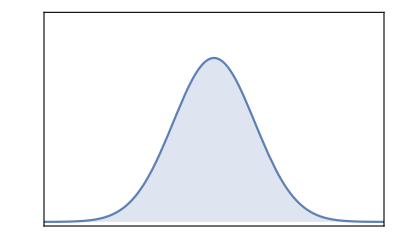

```mathematica
plotNorm = Show[
Plot[PDF[NormalDistribution[0, 1], x], {x, -5, 5}, Filling->Axis],
Frame->True,
FrameTicks->{{{#, MaTeX[#,Magnification->1.5]}&/@{0, 0.2, 0.4}, None}(* y-ticks *), {{#, MaTeX[#,Magnification->1.5]}&/@{-4, -2, 0, 2, 4}, None} (* x-ticks *)},
FrameLabel->{MaTeX["y", Magnification->1.5], MaTeX["P_Y(y)", Magnification->1.5]
(*,MaTeX["\\text{Test data}", Magnification->1.5]*)},
PlotRangePadding->None,
PlotRange->{{-4, 4},{0, 0.5}}
]
```

```mathematica
Export[NotebookDirectory[]<>"imgs/bump.svg", plotNorm]
```

/home/denys/Documents/ifw/ml/datasciencesnippets/gpr/imgs/bump.svg

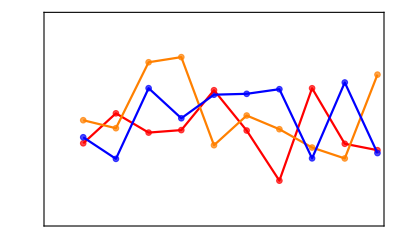

```mathematica
GaussSamplePoints1 = {#,  RandomReal[NormalDistribution[0, 1],  1]⟦1⟧}&/@Range[10];
GaussSamplePoints2 = {#,  RandomReal[NormalDistribution[0, 1],  1]⟦1⟧}&/@Range[10];
GaussSamplePoints3 = {#,  RandomReal[NormalDistribution[0, 1],  1]⟦1⟧}&/@Range[10];
GaussVectors = Show[
ListPlot[GaussSamplePoints1,  PlotMarkers->{markerDisk[Red], 0.05}],
ListPlot[GaussSamplePoints2,  PlotMarkers->{markerDisk[Orange], 0.05}],
ListPlot[GaussSamplePoints3,  PlotMarkers->{markerDisk[Blue], 0.05}],
ListLinePlot[GaussSamplePoints1, PlotStyle->Red],
ListLinePlot[GaussSamplePoints2, PlotStyle->Orange],
ListLinePlot[GaussSamplePoints3, PlotStyle->Blue],
Frame->True,
FrameTicks->{{{#, MaTeX[#,Magnification->1.25]}&/@{-4,-2, 0, 2, 4}, None}(* y-ticks *), {{#, MaTeX[#,Magnification->1.25]}&/@{0, 1,2, 3,4, 5,6, 7, 8,9,10}, None} (* x-ticks *)},
FrameLabel->{MaTeX["\\text{Variable index}", Magnification->1.25], MaTeX["y", Magnification->1.25]
(*,MaTeX["\\text{Test data}", Magnification->1.5]*)},
PlotRangePadding->None,
PlotRange->{{0, 10},{-4,4}}
]
```

```mathematica
Export[NotebookDirectory[]<>"imgs/gauss_vecs.svg", GaussVectors]
```

/home/denys/Documents/ifw/ml/datasciencesnippets/gpr/imgs/gauss_vecs.svg

### Kernel Correlation Matrix

```mathematica
RBFKernel[x_, y_,l_,σ_]:=σ^2 Exp[(-(x - y)^2)/(2 l^2)];
RBFCorrelationMatrix[x1_, x2_, l_, σ_]:=Module[{matrix},
matrix = Quiet@Table[RBFKernel[x1⟦i⟧, x2⟦j⟧, l, σ], {i, Length@x1}, {j, Length@x2}];
matrix
]
MakeMatrixPlot[xs_, l_, σ_]:=Module[{plot},
plot= MatrixPlot[
RBFCorrelationMatrix[xs, xs, l, σ],
PlotRangePadding->None,
ColorFunction->"BlueGreenYellow",
ColorFunctionScaling->False
];
plot
]
```

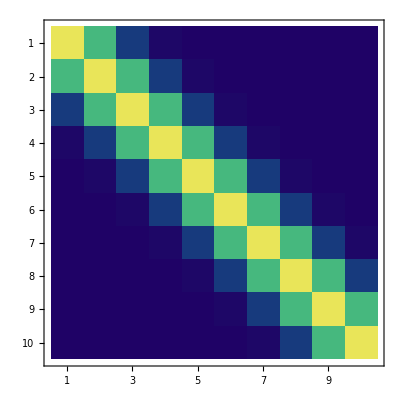

```mathematica
NN=10;
xs= Range[NN];
MakeMatrixPlot[xs, 1, 1]
```

```mathematica
Manipulate[
MakeMatrixPlot[xs, l, σ],
{{l, 1}, 0.001, 5, 0.1, Appearance->"Open"},
{{σ, 1}, 0, 5, 0.1, Appearance->"Open"}
]
```

```mathematica
μ = {0,0};
Σ = {{1, 0.8},{0.8, 1}};

μ10 = Table[0, {i, Length@xs}];
Σ10 = RBFCorrelationMatrix[xs, xs, 1, 1];

PlotMultinormal2D[μ1_, μ2_, σ11_,σ12_, σ21_,σ22_]:=Module[{plot},
plot =Show[
 ContourPlot[
PDF[MultinormalDistribution[{μ1, μ2},{{σ11, σ12}, {σ21, σ22}}], {x, y}], 
{x, -3,3}, {y, -3, 3},
PlotPoints->7,
(*MeshFunctions->{#3&,#3&},
Mesh->{Range[0,1,0.4],Range[0,0.8,0.4]},
MeshStyle->{Black,Dashed},*)
ColorFunction->"Rainbow",
PlotRange->All
],
Frame->True,
PlotRangePadding->None,
(*FrameTicks->None
,*) FrameTicks->{{{#, MaTeX[#,Magnification->1.5]}&/@{-4, -2, 0, 2, 4}, None}, {{#, MaTeX[#,Magnification->1.5]}&/@{-4, -2, 0, 2, 4}, None}},
FrameLabel->{MaTeX["y_1", Magnification->1.5], MaTeX["y_2", Magnification->1.5]}
];
plot
]
Make2DPlot[points_]:=Module[{plot},
plot=Show[
ListPlot[points, PlotRange->{-4, 4},  PlotMarkers->{markerDisk[Blue], 0.05}],
ListLinePlot[points, PlotRange->{-4, 4}],
Frame->True,
FrameTicks->False(*,
FrameTicks->{{{#, MaTeX[#,Magnification->1.5]}&/@{-4, -2, 0, 2, 4}, None},
 {{#, MaTeX[#,Magnification->1.5]}&/@Range[Length@points], None}},
FrameLabel->{MaTeX["\\text{Variable index}", Magnification->1.5], MaTeX["y", Magnification->1.5]},*)
,AspectRatio->1
];
plot
]

PlotSampledPoints[μ_, Σ_]:=Module[{points, pointsY,plot, lineStyle, lines, covMatrixPlot,priorPlot, Gaussian2D},
pointsY = Flatten[RandomReal[MultinormalDistribution[μ,Σ], 1], 1];
points={#,pointsY⟦#⟧}&/@Range[Length@pointsY];
lineStyle={White, Dashed};
lines={
Line[{{-4, pointsY⟦2⟧},{pointsY⟦1⟧, pointsY⟦2⟧}}],
Line[{{pointsY⟦1⟧, -4},{pointsY⟦1⟧, pointsY⟦2⟧}}]
};
covMatrixPlot = MatrixPlot[Σ,
PlotRangePadding->None,
ColorFunction->"BlueGreenYellow",
ColorFunctionScaling->False,
FrameTicks->None
];
priorPlot= Make2DPlot[points];
Gaussian2D= Show[
PlotMultinormal2D[μ⟦1⟧,μ⟦2⟧,Σ⟦1,1⟧,Σ⟦1,2⟧,Σ⟦2,1⟧,Σ⟦2,2⟧],
ListPlot[{{pointsY⟦1⟧, pointsY⟦2⟧}},  
PlotMarkers->{markerDisk[White], 0.04}],
Epilog->{Directive[lineStyle], lines}
];
(* print covariance matrix *)
(*Print[{{Σ⟦1,1⟧//N,Σ⟦1,2⟧//N},{Σ⟦2,1⟧//N,Σ⟦2,2⟧//N}}];*)

plot =GraphicsGrid[
{
{priorPlot, SpanFromLeft, covMatrixPlot},
{SpanFromAbove, SpanFromBoth, Gaussian2D}
},
ImageSize->500
];
plot
]
```

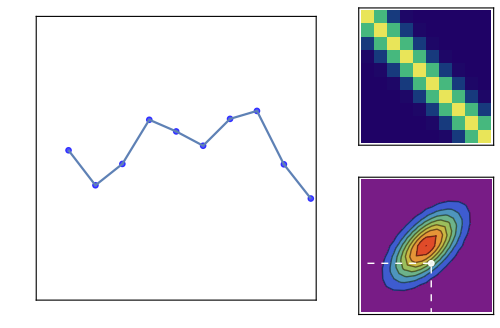

```mathematica
prior = PlotSampledPoints[0&/@Range[Length@xs],RBFCorrelationMatrix[xs, xs, 1,1]]
```

```mathematica
Export[NotebookDirectory[]<>"imgs/prior.svg", prior]
```

/home/denys/Documents/ifw/ml/datasciencesnippets/gpr/imgs/prior.svg

```mathematica
Manipulate[
PlotSampledPoints[0&/@Range[NN],RBFCorrelationMatrix[xs, xs, l, σ]],
{{l, 1}, 0.001, 5, 0.2, Appearance->"Open"},
{{σ, 1}, 0.001, 5, 0.2, Appearance->"Open"}
]
```

{{0.641601,0.29432},{0.29432,0.641601}}

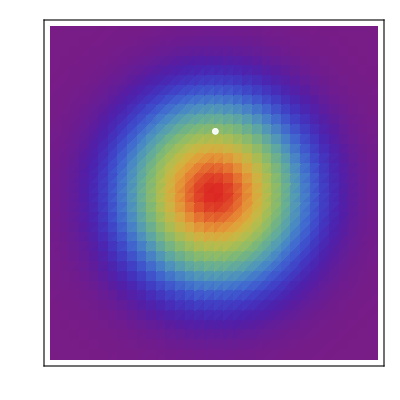

```mathematica
Show[
PlotMultinormal2D[0,0,1,0,0,1],
ListPlot[RandomReal[MultinormalDistribution[{0, 0},{{1, 0.8}, {0.8, 1}}], 1],  
PlotMarkers->{markerDisk[White], 0.04}]
]
```

```mathematica
Manipulate[
PlotMultinormal2D[μ1,μ2,1,σ12,σ12,1],
{{μ1, 0}, 0, 5, 0.1, Appearance->"Open"},
{{μ2, 0}, 0, 5, 0.1, Appearance->"Open"},
{{σ12, 0}, 0, 0.9, 0.1, Appearance->"Open"}
]
```